IGraph/M 0.3.108 (December 17, 2018)

Evaluate IGDocumentation[] to get started.

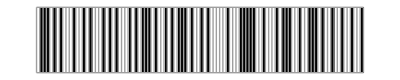

Evaluate ButtonBox[RowBox[{"IGDocumentation", "[", "]"}],BaseStyle->"Link",ButtonData->"paclet:IGraphM"] to get started.

4

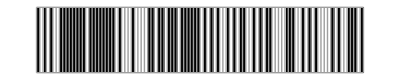

```mathematica
<<IGraphM`
ClearAll[graph];
Nn=(10)^2;(*number of spins*)mcs=50;(*Monte Carlo steps*)J=1;(*interaction strength*)
graph = IGSquareLattice[{Sqrt[Nn],Sqrt[Nn]},Periodic->True];
(*graph = IGErdosRenyiGameGNM[Nn,Nn*4];*)
(*graph = IGCompleteAcyclicGraph[Nn];*)
myA =AdjacencyMatrix[graph];
b=0;
kT=Range[4,1,-0.2];(*range of temperatures*)NkT=Length[kT];
bσ=RandomChoice[{1,-1},Nn];(*random initial state*)
(* okay il top sarebbe definire una matrice quadrata *)
Mt=0;M2t=0;Mt0=0;M2t0=0;(*inizialisation of<M>and<M^2>*)
χT=Table[0,{k,1,NkT}];(*inizialisation of χ*)
Mtvett = Table[0,{i,1,NkT}];
h=0;
myH[σ_,myA_]:= For[k=1,k<Nn,k++,
				h = h - b*σ[[k]]; 
				For[j=1, j < Nn,j++,
				h = -J*σ[[k]]*σ[[j]]*myA[[k]][[j]] + h;];
				   k++];

myH[bσ,myA];
hOld = h;
h = 0;
(* step iniziale per la h *)
time = Table[Table[0,{jj,1,Nn}],{j,1,mcs+1}];
time[[1]]=Table[bσ[[jj]],{jj,1,Nn}];
ArrayPlot[{1/2 (bσ+1)},Mesh->All]
```

```mathematica
(* Glauber update *)
bσ=RandomChoice[{1,-1},Nn];(*random initial state*)
For[iT = 1, iT <=NkT, iT++,
β=1/kT[[iT]];(*β=1/kT*)
For[kk=2,kk≤mcs+1,kk++,
(*Monitor[*)
For[t=1,t≤Nn,t++,
(*loop over Monte Carlo steps*)(*choose the spin to flip*)
xflip=RandomInteger[{1,Nn}];
(*acceptance step*)
flipped = bσ;
flipped[[xflip]] = -flipped[[xflip]] ;
myH[flipped,myA];
deltaH = (h - hOld);
α=Min[1,1/(1+Exp[2*β deltaH])];
α=Min[1,Exp[-β (deltaH)]];
u=RandomReal[{0,1}];
If[u≤α,tt=bσ[[xflip]];
hOld = h;
h = 0;
bσ[[xflip]]=-tt,h = 0;
];];(*end For i*)(*calculate<M>and<M^2>*)
(*plot=ArrayPlot[{1/2 (bσ+1)},Mesh->All];*)
Mt = (Mt0(kk-1)+Total[bσ])/kk; Mt0 = Mt;
 M2t = (M2t0(kk-1)+Total[bσ]^2)/kk; M2t0 = M2t; 
(*Print["End of the ",kk," mcs iteration"];*)
];
Mtvett[[iT]] = Mt;
χT[[iT]] = β(M2t - Mt^2);
Print["End of the ",iT," full iteration"];
]
(*,plot];*)
(*time[[kk]]=Table[bσ[[jj]],{jj,1,Nn}];*)
(*ArrayPlot[{1/2 (bσ+1)},Mesh->All]*)
```

End of the 1 full iteration

End of the 2 full iteration

End of the 3 full iteration

End of the 4 full iteration

End of the 5 full iteration

End of the 6 full iteration

End of the 7 full iteration

End of the 8 full iteration

End of the 9 full iteration

End of the 10 full iteration

End of the 11 full iteration

End of the 12 full iteration

End of the 13 full iteration

End of the 14 full iteration

End of the 15 full iteration

End of the 16 full iteration

-198

0

4

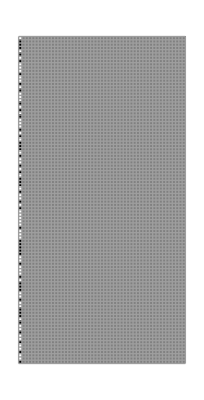

```mathematica
hOld
h	
deltaH
(*myH[flipped,myA]
h
bσ
flipped
deltaH*)
ArrayPlot[1/2 (Transpose[time]+1),Mesh->All]

(* evoluzione della rete nel tempo: x tempo, y val H*)
(* attenzione non sono vicini*)
(*visualizzazione della rete..*)
```

```mathematica
<<IGraphM`
```

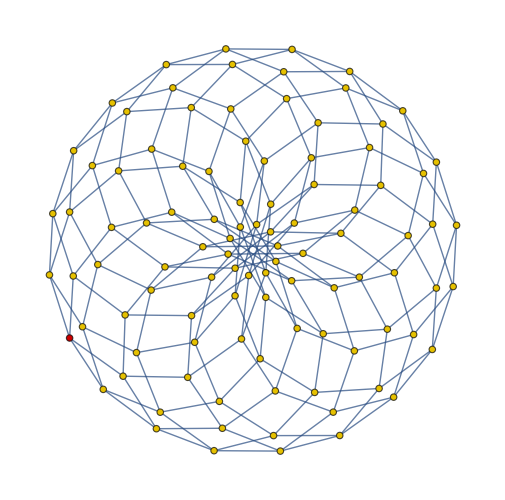

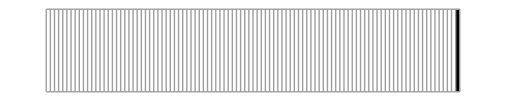

```mathematica
vettW = Table[0,{mj,1,Nn}];
vettB = Table[0,{j,1,Nn}];
k=0; j = 1; l = 1;
For[k=1,k <= Nn,k++,
If[bσ[[k]] == 1,vettW[[j]]=k; j++,vettB[[l]]=k;l++]]
HighlightGraph[graph,{vettW,vettB}]
ArrayPlot[{1/2 (bσ+1)},Mesh->All] (* okay, visualizza da sx verso alto, prima colonna, poi seconda colonna e così via*}
```

```mathematica
Print["value was changed"];
```

value was changed

```mathematica
myH[σ_,myA_]:= For[k=1,k<Length[myA], 
				For[j=1, j < Length[myA],
				h = σ[[k]]*σ[[j]]*myA[[k]][[j]] + h;
				j++;];
				   k++];
```

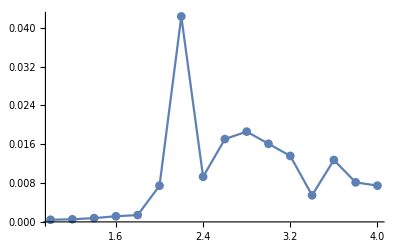

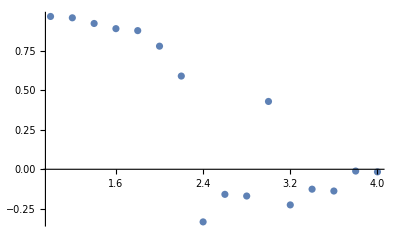

{1,1,1,1,1,1,1,1,1,1,1}

```mathematica
plotME = Table[{kT[[i]],χT[[i]]/Nn^2},{i,1,NkT}];
(*plotMMe = Table*)
ListPlot[plotME,Joined->True,PlotMarkers->Automatic]
plotEM = Table[{kT[[i]],Mtvett[[i]]/Nn},{i,1,NkT}];
ListPlot[plotEM]
```

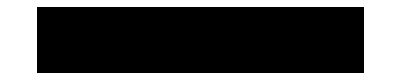

1

```mathematica
ArrayPlot[{bσ}]
```